# Neural Logic Networks

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

## A regression problem

```mathematica
data=ResourceData["7307b047-05ec-4d46-b3c9-9995faf75130"]
```

Dataset[<>]

```mathematica
{trainData,testData}=[data,"TestSetSize"->Scaled[0.1],"Shuffle"->True];
```

## Utilities

### Feature encoders

```mathematica
FeatureValues[data_]:=Block[{features=Normal[Keys@First[data]],featureValues},
featureValues={#,Normal[DeleteDuplicates[data[All,#]]]}&/@features;
Association[First[#]->Last[#]&/@featureValues]
]
featureValues=FeatureValues[trainData];
```

```mathematica
encoders=Map[RealEncoderDecoder[#, 32]&,featureValues];
```

```mathematica
standardNetInputSize=Length[encoders]-1
```

11

```mathematica
standardFeatureLayer=Block[{inputEncoders=Drop[Normal[encoders],1]},NetGraph[
<|
Splice[Map[#->ReshapeLayer[{1},"Input"->{}]&,Keys[inputEncoders]]],
"Catenate"->CatenateLayer["Output"->standardNetInputSize]
|>,
Join[
Map[#->"Catenate"&,Keys[inputEncoders]],
Map[NetPort[#]->#&,Keys[inputEncoders]]
]
]]
```

NetGraph[<>]

```mathematica
neuralLogicFeatureLayer=Block[{inputEncoders=Drop[Normal[encoders],1]},NetGraph[
<|"Catenate"->CatenateLayer[]|>,
Map[NetPort[#]->"Catenate"&,Keys[inputEncoders]],
Sequence@@Normal[Drop[Normal[#["NetEncoder"]&/@encoders],1]]
]]
```

NetGraph[<>]

```mathematica
exampleInputFeature=neuralLogicFeatureLayer[Normal[Drop[trainData[[1]],1]]]
```

{0.,0.,0.,1.,1.,1.,1.,0.,0.,0.,1.,0.,0.,1.,0.,0.,0.,1.,0.,1.,1.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,1.,1.,1.,1.,0.,0.,0.,1.,0.,1.,0.,0.,0.,1.,0.,0.,1.,1.,1.,0.,0.,0.,0.,1.,1.,1.,0.,0.,0.,0.,0.,1.,1.,1.,1.,0.,0.,0.,0.,1.,1.,1.,1.,0.,0.,1.,0.,1.,1.,0.}

```mathematica
neuralLogicInputSize=Length[exampleInputFeature]
```

84

### Define standard net

```mathematica
StandardNet[]:=Module[{standardNet},
standardNet=NetChain[{
LinearLayer[256,"Input"->standardNetInputSize],
ElementwiseLayer["ScaledExponentialLinearUnit"],
LinearLayer[256],
ElementwiseLayer["ScaledExponentialLinearUnit"],
LinearLayer[256],
ElementwiseLayer["ScaledExponentialLinearUnit"],
LinearLayer[1]
}];
NetGraph[
<|
"Features"->standardFeatureLayer,
"Net"->standardNet,
"Reshape"->ReshapeLayer[{}]
|>,
{"Features"->"Net","Net"->"Reshape",NetPort["Reshape","Output"]->NetPort["WineQuality"]}
]
]
```

### Train standard net

```mathematica
TrainStandardNet[net_,trainData_,testData_]:=NetTrain[net,trainData,All,
ValidationSet->testData,
MaxTrainingRounds->Infinity,
Method->{"ADAM"},
TargetDevice->"GPU",
WorkingPrecision->"Real32"]
```

### Evaluate standard net

```mathematica
NetPredict[trainedNet_,data_,targetName_]:=Module[{prediction},
prediction=ResourceFunction["DynamicMap"][<|
"Prediction"->trainedNet[#],
"Target"->#[targetName]
|>&,
Normal[data]
]
]
```

```mathematica
GetStandardWeights[trainedStandardNet_]:=Module[{},
Flatten[Normal/@DeleteMissing[Values[Quiet[NetExtract[NetFlatten[trainedStandardNet],{All,"Weights"}]]]]]
]
```

### Define neural logic net

```mathematica
NeuralLogicPredictor[size_]:=HardNeuralChain[{
HardNeuralNOR[neuralLogicInputSize,size,RandomNormalSoftBits[#]&,RandomNormalSoftBits[#]&],
HardNeuralNAND[size,size,RandomNormalSoftBits[#]&,RandomNormalSoftBits[#]&],
HardNeuralNOR[size,size,RandomNormalSoftBits[#]&,RandomNormalSoftBits[#]&],
HardNeuralReshapeLayer[size,size/3],
NeuralHardeningLayer[],
{AggregationLayer[Mean,1],#&}
}]
```

```mathematica
NeuralLogicPredictor[size_]:=HardNeuralChain[{
HardNeuralNOT[neuralLogicInputSize,size,RandomNormalSoftBits[#]&],
HardNeuralMajority[size,neuralLogicInputSize],
HardNeuralNOT[size,size,RandomNormalSoftBits[#]&],
HardNeuralMajority[size,size],
HardNeuralNOT[size,encoders["WineQuality"]["NumBits"],RandomNormalSoftBits[#]&],
HardNeuralMajority[encoders["WineQuality"]["NumBits"],size]
}]
```

```mathematica
NeuralLogicPredictor[size_]:=HardNeuralChain[{
HardNeuralNOT[neuralLogicInputSize,size],
HardNeuralOR[neuralLogicInputSize,size],
HardNeuralNOT[size,size],
HardNeuralAND[size,size],
HardNeuralReshapeLayer[size,encoders["WineQuality"]["NumBits"]],
NeuralHardeningLayer[],
{AggregationLayer[Mean],#&}
}]
```

```mathematica
(* Best candidate *)
NeuralLogicPredictor[size_]:=HardNeuralChain[{
HardNeuralNAND[neuralLogicInputSize,size],
HardNeuralNAND[size,size],
HardNeuralReshapeLayer[size,encoders["WineQuality"]["NumBits"]],
NeuralHardeningLayer[{encoders["WineQuality"]["NumBits"],size/encoders["WineQuality"]["NumBits"]}],
{AggregationLayer[Mean],#&}
}]
```

```mathematica
NeuralLogicPredictor[size_]:=HardNeuralChain[{
HardNeuralNOR[neuralLogicInputSize,size],
HardNeuralNOR[size,size/2],
HardNeuralNOR[size/2,size/4],
HardNeuralNOR[size/4,size/8],
HardNeuralFlattenLayer[],
{BinaryCountToRealLayer[size/8,encoders["WineQuality"]["MinMax"]],#&}
}]
```

```mathematica
NetFlatten[NeuralLogicPredictor[40*3][[1]]]
```

NetGraph[<>]

```mathematica
NeuralLogicNet[size_]:=Module[{softNet,hardNet,net,trainableNet},
{softNet,hardNet}=NeuralLogicPredictor[size];
trainableNet=NetGraph[
<|
"FeatureLayer"->neuralLogicFeatureLayer,
"SoftNet"->softNet(*,
"Hardening"->HardeningLayer[encoders["WineQuality"]["NumBits"]]*)
|>,
{
"FeatureLayer"->"SoftNet",(*,
"SoftNet"->"Hardening"*)
NetPort["SoftNet","Output"]->NetPort["WineQuality"]
}
];
{trainableNet,hardNet}
]
```

```mathematica
NetFlatten[NeuralLogicNet[30][[1]]]
```

NetGraph[<>]

### Train neural logic net

```mathematica
HardRegressionLossLayer[size_,targetName_,targetEncoder_]:=NetGraph[
<|
"Loss"->With[{a=Map[2^#&,Range[size-1,0,-1]]},
FunctionLayer[
a(#Input -#Target )^2&
]
]
|>,
{
NetPort[targetName]->NetPort["Loss","Target"]
},
targetName->targetEncoder
]
```

```mathematica
HardRegressionLossLayer[8,"WineQuality",encoders["WineQuality"]["NetEncoder"]]
```

NetGraph[<>]

```mathematica
TrainNeuralLogicNet[net_,trainData_,testData_]:=NetTrain[net,trainData,All,
ValidationSet->testData,
(*LossFunction->MeanSquaredLossLayer["Target"->encoders["WineQuality"]["NetEncoder"]],*)
(*LossFunction->HardRegressionLossLayer[encoders["WineQuality"]["NumBits"],"WineQuality",encoders["WineQuality"]["NetEncoder"]],*)
Method->{"ADAM"},
TargetDevice->"GPU",
WorkingPrecision->"Real64",
MaxTrainingRounds->Infinity]
```

### Evaluate neural logic net

```mathematica
GetNeuralLogicWeights[trainedNeuralLogicNet_]:=Harden[Flatten[ExtractWeights[trainedNeuralLogicNet]]]
```

## A standard neural network

```mathematica
(*
p=Predict[trainData->"WineQuality",PerformanceGoal->"Quality",Method->"NeuralNetwork"];
pm=PredictorMeasurements[p,testData]
*)
```

```mathematica
standardNet=StandardNet[]
```

NetGraph[<>]

```mathematica
result=TrainStandardNet[standardNet,trainData,testData];
```

```mathematica
trainedStandardNet=result["TrainedNet"];
```

```mathematica
NetMeasurements[trainedStandardNet,testData,{"RSquared","FractionVarianceUnexplained" ,"MeanDeviation","MeanSquare","StandardDeviation"}]
```

{0.28406,0.71594,0.620504,0.614486,0.783891}

```mathematica
standardPredictions=NetPredict[trainedStandardNet,testData,"WineQuality"];
```

```mathematica
{MinMax[#["Prediction"]&/@standardPredictions],MinMax[#["Target"]&/@standardPredictions]}
```

{{4.50466,6.92936},{3,9}}

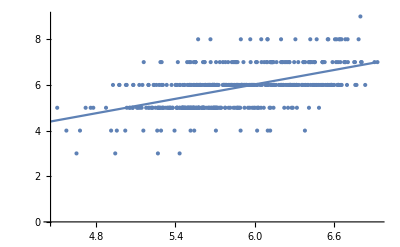

```mathematica
ResourceFunction["RegressionListPlot"][Values/@standardPredictions]
```

```mathematica
standardWeights=GetStandardWeights[trainedStandardNet];
```

```mathematica
standardNetSize=Quantity[Length[standardWeights]*32/1024.0,"Kilobytes"]
```

2144. kB

## A neural logic network

```mathematica
{softNet,hardNet}=NeuralLogicNet[3*64];
```

```mathematica
NetFlatten[softNet]
```

NetGraph[<>]

```mathematica
Length[trainData]
```

4408

```mathematica
result=Block[{td=trainData,vd=testData},
TrainNeuralLogicNet[softNet,td,vd]
];
```

```mathematica
(*trainedNeuralLogicNet=NetGraph[{1->result["TrainedNet"],2->SoftBitVectorToRealLayer[encoders["WineQuality"]["NumBits"],encoders["WineQuality"]["MinMax"]]},{1->2,NetPort[2,"Output"]->NetPort["WineQuality"]}]*)
trainedNeuralLogicNet=result["TrainedNet"]
```

$Failed[TrainedNet]

```mathematica
NetMeasurements[trainedNeuralLogicNet,testData,{"RSquared","FractionVarianceUnexplained" ,"MeanDeviation","MeanSquare","StandardDeviation"}]
```

{-0.140051,1.14005,0.704939,0.830732,0.911445}

```mathematica
neuralLogicPredictions=NetPredict[trainedNeuralLogicNet,testData,"WineQuality"];
```

```mathematica
{MinMax[#["Prediction"]&/@neuralLogicPredictions],MinMax[#["Target"]&/@neuralLogicPredictions]}
```

{{4.46,7.32},{3,9}}

```mathematica
Sort/@{DeleteDuplicates[#["Prediction"]&/@neuralLogicPredictions],DeleteDuplicates[#["Target"]&/@neuralLogicPredictions]}
```

{{4.46,4.48,4.5,4.56,4.58,4.72,4.74,4.76,4.82,4.84,4.86,4.9,4.92,4.94,4.96,4.98,5.,5.02,5.04,5.08,5.1,5.12,5.14,5.16,5.18,5.2,5.22,5.24,5.26,5.28,5.3,5.32,5.34,5.36,5.38,5.4,5.42,5.44,5.46,5.48,5.5,5.52,5.54,5.56,5.58,5.6,5.62,5.64,5.66,5.68,5.7,5.72,5.74,5.76,5.78,5.8,5.82,5.84,5.86,5.88,5.9,5.92,5.94,5.96,5.98,6.,6.02,6.04,6.06,6.08,6.1,6.12,6.14,6.16,6.18,6.2,6.22,6.24,6.26,6.28,6.3,6.32,6.34,6.36,6.38,6.4,6.42,6.44,6.46,6.48,6.5,6.52,6.54,6.56,6.58,6.6,6.64,6.66,6.68,6.72,6.74,6.76,6.78,6.8,6.84,6.86,6.88,6.9,6.92,6.94,7.,7.12,7.14,7.18,7.32},{3,4,5,6,7,8,9}}

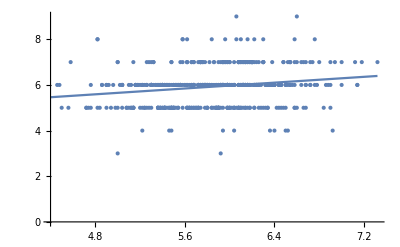

```mathematica
ResourceFunction["RegressionListPlot"][Values/@neuralLogicPredictions]
```

```mathematica
hnf=HardNetFunction[hardNet,trainedNeuralLogicNet];
hnbe=HardNetBooleanExpression[hnf,neuralLogicInputSize]
```

```mathematica
encoders["WineQuality"]["DecoderFunction"]
```

SoftBitVectorToReal[Normal[#1],{3,9}]&

```mathematica
NeuralLogicPredict[data_,encoders_,targetName_,hardNetFunction_,featureLayer_]:=Module[{booleanPrediction},
booleanPrediction=ResourceFunction["DynamicMap"][<|
"Prediction"->N[encoders["WineQuality"]["DecoderFunction"][Boole[hardNetFunction[Harden[Normal[featureLayer[#]]]]]]],
"Target"->#[targetName]
|>&,
Normal[data]
]
]
```

```mathematica
predictions=NeuralLogicPredict[testData,encoders,"WineQuality",hnf,neuralLogicFeatureLayer]
```

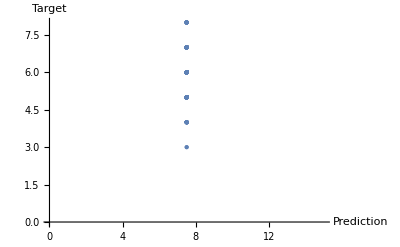

```mathematica
ListPlot[predictions,AxesLabel->Automatic]
```

```mathematica
neuralLogicWeights=GetNeuralLogicWeights[result["TrainedNet"]];
```

```mathematica
neuralLogicNetSize=Quantity[Length[neuralLogicWeights]/8/1024//N,"Kilobytes"]
```

29.3438 kB

```mathematica
standardNetSize/neuralLogicNetSize
```

80.

## Notes

```mathematica
bctr=BinaryCountToReal[{0,1000}];
```

```mathematica
bctr[{1,1,1,1,0,0,0,0,0,0,1,1,1}]
```

{538.462}

```mathematica
bctrl=BinaryCountToRealLayer[13,{0,1000}]
```

NetGraph[<>]

```mathematica
bctrl[{1,1,1,1,0,0,0,0,0,0,1,1,1}]
```

538.462

```mathematica
bctrl[{0.8,0.52,0.6,0.85,0.1,0.2,0.3,0.4,0.45,0.49,0.99,0.65,0.62}]
```

538.462

```mathematica
{1,0,0,1,0,0,1,1}{128,64,32,16,8,4,2,1}
```

{128,0,0,16,0,0,2,1}

```mathematica
btr=BinaryToReal[8,{0.0,255.0}];
```

```mathematica
btr[{1,0,0,0,0,0,0,0}]
```

{255.}

```mathematica
btr[{1,0,0,0,0,1,1,0}]
```

{255.}

```mathematica
btr[{0,1,1,1,1,0,0,0}]
```

{239.063}

```mathematica
sbvtrl=SoftBitVectorToRealLayer[8,{0,255}]
```

NetGraph[<>]

```mathematica
{btr[{0,1,1,1,1,0,0,0}],sbvtrl[{0,1,1,1,1,0,0,0}]}
```

{{239.063},239.063}

```mathematica
{btr[Boole[Harden[{0.1,0.6,0.6,0.6,0.6,0,0,0}]]],sbvtrl[{0.1,0.6,0.6,0.6,0.6,0,0,0}]}
```

{{239.063},239.063}